# 1 - Playing with new things

### 1.1 - Virtual Book

```mathematica
r=√(({{x, y, z}}).({{x}, {y}, {z}}))
```

(√(x^2+y^2+z^2))

```mathematica
f[ρ_]:=ρ^2
f[r]
Clear[f]
```

(x^2+y^2+z^2)

### 1.2 - Some Example Problems

#### 1.2.1 - Calculating the probability of an increase in entropy (Ph127a)

```mathematica
n = 10^3;
T1 = 90;
T2 = 100;
U10 = -6.85*10^-23;
U20 = -6.16*10^-23;
me = 9.11*10^-31;
qe = 1.6*10^-19;
hbar = 1.05*10^-34;

gamma = qe*hbar/me;

x0 = (1/Sqrt[2*n])*(U20-U10)/gamma ;

P = (2/Sqrt[Pi])*NIntegrate[Exp[-x^2],{x,x0,Infinity}]
```

0.99056

#### 1.2.2 - Estimating the binding energy of N_2(Ph127a)

```mathematica
h = 6.63*^-34;
T= 3000*(1.381*^-23);
oϵ = 5*(1.6*^-19);
nϵ = 9.5*(1.6*^-19);
o3ϵ = 6.5*(1.6*^-19);
oi = 2*(2.657*^-26)*(5*^-11)^2;
ni = 2*(2.326*^-26)*(5*^-11)^2;
om = (2.7*^-26);
nm = (2.3*^-26);
pa = (1*^5);
on = 0.2 * pa / T;
nn = 0.8 * pa / T;
NSolve[(on - x)/(2*x^2) == 8* Pi^2*(oi*T*h)/(Pi*om*T)^(3/2)*Exp[oϵ/T], x]
```

{{x→-2.75377×10^22},{x→2.60516×10^22}}

#### 1.2.3 - “Proof” all odd derivatives of a function are zero (Ph127a)

```mathematica
Do[Print[D[1/Sqrt[t^2-x^2],{x,n}]/.x->0], {n,1,51,2}]
```

0

0

0

«23 more identical outputs»

## 2 - Series functions

### 2.1 - Expansions of Sin and Cos

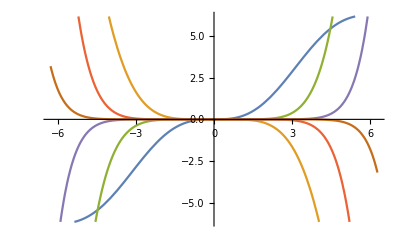

```mathematica
Clear[x,n]
SerCos[x_,n_]:=Normal[Series[Cos[y],{y,0,n}]]/.y->x;
SerSin[x_,n_]:=Normal[Series[Sin[y],{y,0,n}]]/.y->x;

Plot[Evaluate[Table[SerSin[x,n]-Sin[x],{n,1,12,2}]],{x,-2π,2π}]
```

As n increases, the approximation error remains nominal for an increasing range of x. For increasing n, the sign of the error alternates in sign.

### 2.2 - Cos^2(x)+Sin^2(x)

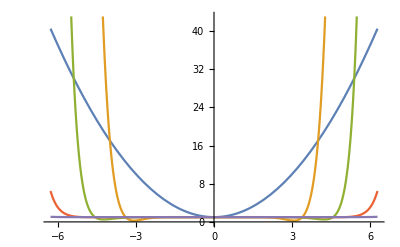

```mathematica
Clear[x,n]

Plot[Evaluate[Table[SerSin[x,n]^2+SerCos[x,n]^2,{n,1,20,4}]],{x,-2π,2π}]
```

As n increases, the approximation remains at 1 for a larger range of x. This is only true at x=0 for n=1. For small n, the series diverges as x increases due as higher order terms are introduced, but not properly accounted for, by multiplying two separate expansions of sin(x) and cos(x) together; i.e. there are terms of order n^2in the expression from the multiplication, but are incorrect as the expansion before multiplication does not take the others that should appear into account.

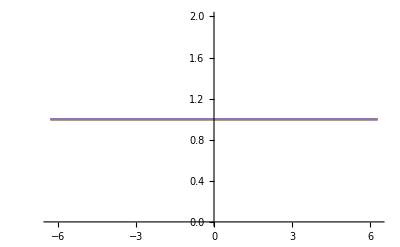

```mathematica
Clear[x,n]
SerCosSq[x_,n_]:=Normal[Series[Cos[y]^2,{y,0,n}]]/.y->x;
SerSinSq[x_,n_]:=Normal[Series[Sin[y]^2,{y,0,n}]]/.y->x;

Plot[Evaluate[Table[SerSinSq[x,n]+SerCosSq[x,n],{n,1,20,4}]],{x,-2π,2π}]
```

This method correctly accounts for the terms of every order so gives the right answer.

## 3 - Matrix Rotations

### 3.1 - Rotation matrices

```mathematica
Rx[x_]:=({{1, 0, 0}, {0, Cos[x], -Sin[x]}, {0, Sin[x], Cos[x]}});
Rz[x_]:=({{Cos[x], -Sin[x], 0}, {Sin[x], Cos[x], 0}, {0, 0, 1}});
```

```mathematica
Rx[θ]
Rx[ζ]
Rz[ϕ]
```

(1 | 0 | 0
0 | cos(θ) | -sin(θ)
0 | sin(θ) | cos(θ))

(1 | 0 | 0
0 | cos(ζ) | -sin(ζ)
0 | sin(ζ) | cos(ζ))

(cos(ϕ) | -sin(ϕ) | 0
sin(ϕ) | cos(ϕ) | 0
0 | 0 | 1)

### 3.2 - General Rotation Matrix

```mathematica
Rot3[ψ_,θ_,ϕ_]:=Rz[ψ].Rx[θ].Rz[ϕ]
```

```mathematica
Simplify[Rot3[ψ,θ,ϕ]]
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | -cos(ψ) sin(ϕ)-cos(θ) cos(ϕ) sin(ψ) | sin(θ) sin(ψ)
cos(θ) cos(ψ) sin(ϕ)+cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ψ) sin(θ)
sin(θ) sin(ϕ) | cos(ϕ) sin(θ) | cos(θ))

### 3.3 - Manual Inverse

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]:=Rz[-ϕ].Rx[-θ].Rz[-ψ]
Simplify[Rot3Inverse[ψ,θ,ϕ].Rot3[ψ,θ,ϕ]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

### 3.4 - Handy Mathematica Inverse

```mathematica
Simplify[Inverse[Rot3[ψ,θ,ϕ]].Rot3[ψ,θ,ϕ]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Clearly both methods produce the identity matrix - as expected.